-Graphics- |   Métodos Computacionales en Álgebra para Informáticos
Matemática Discreta y Lógica
Dpto. de Matemáticas. Área de  Álgebra  (M. A. García, C. Ordóñez, J. F. Ruiz)

# Capítulo 8 Relaciones binarias y conjuntos ordenados

## 1. Relaciones binarias

### Ejemplo 8.1.

Sean A = {a, b, c, d, e, f, g, h} y R = {(a, a), (b, b), (c, c), (d, d), (e, e), (f, f), (g, g), (h, h), (a, b), (b, a)}. Determinar si R es reflexiva, simétrica, transitiva o antisimétrica, y comprobar si R es relación de orden o de equivalencia.

En primer lugar, evaluaremos la función 8.1.:

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

Y luego introducimos:

```mathematica
A={a,b,c,d,e,f,g,h};
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f},{g,g},{h,h},{a,b},{b,a}};
AnalisisRB[A,R]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{a,b},{b,a}}

R es una relación de equivalencia

R no es relación de orden

### Ejemplo 8.2.

Sean A = {a, b, c, d, e, f, g, h} y R = {{(c, c), (d, d), (e, e), (f, f), (g, g), (h, h), (a, b), (b, a), (b, d), (e, f), (b, e)}. }. Determinar si R es reflexiva, simétrica, transitiva o antisimétrica, y comprobar si R es relación de orden o de equivalencia.

Nuevamente, evaluamos la función 8.1.:

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

Y luego introducimos:

```mathematica
A={a,b,c,d,e,f,g,h};
R={{c,c},{d,d},{e,e},{f,f},{g,g},{h,h},{a,b},{b,a},{b,d},{e,f},{b,e}};
AnalisisRB[A,R]
```

R no es reflexiva, falla en los elementos: {a,b}

R no es simétrica, falla en los pares: {{d,b},{f,e},{e,b}}

R no es transitiva, falla en los pares: {{{b,a},{a,b}},{{a,b},{b,a}},{{a,b},{b,d}},{{b,e},{e,f}},{{a,b},{b,e}}}

R no es antisimétrica, falla en los pares: {{a,b},{b,a}}

R no es relación de equivalencia

R no es relación de orden

## 2. Relaciones de equivalencia

### Ejemplo 8.3.

Calculamos la clase de los tres primeros elementos del conjunto A del ejemplo 8.1.

Cargamos la función 8.2.:

```mathematica
CLASE[A_,R_,a_]:=Module[{CONTADORi},clase={};
Do[If[Intersection[{{A[[CONTADORi]],a}},R]≠{}&&Intersection[{{a,A[[CONTADORi]]}},R]≠{},AppendTo[clase,A[[CONTADORi]]];];,{CONTADORi,1,Length[A]}];
clase];
```

y evaluamos con los datos del ejercicio:

```mathematica
A={a,b,c,d,e,f,g,h};
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f},{g,g},{h,h},{a,b},{b,a}};
CLASE[A,R,a]
CLASE[A,R,b]
CLASE[A,R,c]
```

{a,b}

{a,b}

{c}

### Ejemplo 8.4.

Calculemos ahora el conjunto cociente para el conjunto A del ejemplo 8.1.

Cargamos la función 8.3.:

```mathematica
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];
```

para evaluar con los datos :

```mathematica
A={a,b,c,d,e,f,g,h};
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f},{g,g},{h,h},{a,b},{b,a}};
COCIENTE[A,R]
```

{{a,b},{c},{d},{e},{f},{g},{h}}

### Ejemplo 8.5.

En el conjunto A = {1, 2, 3, 4, 5, 6, 7} se establece la relación de equivalencia R = {(1, 1), (2, 1), (1, 2), (2, 2), (3, 3), (4, 4), (4, 5), (4, 6), (5, 5), (5, 4), (5, 6), (6, 6),(6, 5), (6, 4), (7, 7)}. Calcular el conjunto cociente de A sobre R.

Cargamos la función 8.3. y, posteriormente, los datos:

```mathematica
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];
```

```mathematica
A={1,2,3,4,5,6,7};
R={{1,1},{2,1},{1,2},{2,2},{3,3},{4,4},{4,5},{4,6},{5,5},{5,4},{5,6},{6,6},{6,5},{6,4},{7,7}};
COCIENTE[A,R]
```

{{1,2},{3},{4,5,6},{7}}

### Ejemplo 8.6.

Sea X = {OverBar[1], OverBar[3] } ⊆ ℤ_5={OverBar[0],OverBar[1],  OverBar[2],OverBar[3], OverBar[4] }.
a)	Definir en el conjunto ℤ_5 una partición con dos elementos A1 y A2 siendo A1 = X. Comprobar que lo es. 
b)	Definimos en ℤ_5 la relación binaria:
                                                                                      x R y  ⇔  x,y ∈A1 
o
x,y ∈A2
         Comprobar que R es una relación de equivalencia y calcular  ℤ_5 /R.

a) Para ello tenemos que definir dos subconjuntos A1 y A2 en ℤ_5={OverBar[0],OverBar[1],  OverBar[2],OverBar[3], OverBar[4] }, donde A1 =  X = {OverBar[1], OverBar[3]} . Así, tomamos A2 = {OverBar[0],  OverBar[2], OverBar[4] }

```mathematica
Z5={0,1,2,3,4};
A1={1,3};
A2={0,2,4};
```

Comprobemos que son subconjuntos de X:

```mathematica
SubsetQ[Z5,A1]
SubsetQ[Z5,A2]
```

True

True

No vacíos:

```mathematica
A1≠ {}
A2≠ {}
```

True

True

Disjuntos dos a dos:

```mathematica
DisjointQ[A1,A2]
```

True

La unión de todos es el total

```mathematica
A1∪A2==Z5
```

b) Definimos en ℤ_5 la relación R, incluyendo los pares cuyos dos elementos están en A1 o en A2, como aparece en la definición de R, y evaluamos la función 8.1. para comprobar que es relación de equivalencia:

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

```mathematica
A={0,1,2,3,4};
A1={1,3};
A2={0,2,4};

R={{0,0},{0,2},{0,4},{1,1},{1,3},{2,0},{2,2},{2,4},{3,1},{3,3},{4,0},{4,2},{4,4}};
AnalisisRB[A,R]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{0,2},{0,4},{1,3},{2,0},{2,4},{3,1},{4,0},{4,2}}

R es una relación de equivalencia

R no es relación de orden

Ahora calculamos el conjunto cociente  ℤ_5 /R aplicando el procedimiento 8.2.

```mathematica
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];
```

```mathematica
COCIENTE[A,R]
```

{{0,2,4},{1,3}}

## 3. Relaciones de orden

### Ejemplo 8.7.

Sean  A = {a, b, c, d} y R = {(a, a), (b, b), (c, c), (d, d), (a, b), (b, d)}. Determinar si R es relación de orden.

Evaluaremos la función 8.4. :

```mathematica
ORDEN[A_,R_]:=Module[{falloReflexiva,falloAntisimetrica,falloTransitiva},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

y luego introducimos:

```mathematica
A={a,b,c,d};
R={{a,a},{b,b},{c,c},{d,d},{a,b},{b,d}};
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R no es transitiva, falla en los pares: {{{a,b},{b,d}}}

R no es relación de orden

Así, si queremos obtener un orden, bastará incluir el par {a, d} en la relación anterior. Comprobemos:

```mathematica
A={a,b,c,d};
R={{a,a},{b,b},{c,c},{d,d},{a,b},{b,d},{a,d}};
ORDEN[A,R]
```

R es reflexiva

R es antisimétrica

R es transitiva

R es una relación de orden

### 3.1. Máximos y mínimos

### Ejemplo 8.8.

Sean  A = {a, b, c, d, e, f, g, h, i} y R = {(a, a), (b, b), (c, c), (d, d), (a, b), (b, d)}} un conjunto ordenado con el diagrama de orden de la ilustración 8.1. Calcular máximo y mínimo de A.

Observemos que la relación binaria asociada es:
R = {(a, a), (a, b), (a, c), (a, d), (a, e), (a, f), (a, h), (a, i), (b, b), (b, e), (b, f), (b, h), (b, i), (c, c), (d, d), (d, e), (d, f), (d, h), (d, i), (e, e), (e, f), (e, h), (e, i), (f, f), (f, i), (g, g), (g, i), (h, h), (h, i), (i, i) } es relación de orden.
Utilizando la función 8.5., podemos calcular el máximo:

```mathematica
MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}],,maxi=False;Break[];],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
MAXIMO[A,R]
```

{}

Esto es, no tiene máximo. Ahora, usando la función 8.6.:

```mathematica
MINIMO[A_,R_]:=Module[{minimo,mini,n,m},minimo={};Do[mini=True;
Do[
If[MemberQ[R,{A[[n]],A[[m]]}],,mini=False;Break[];],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];minimo]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
MINIMO[A,R]
```

{}

### 3.2. Elementos maximales y minimales

### Ejemplo 8.9.

Sea A el mismo conjunto ordenado del ejemplo 8.8., calculamos sus elementos maximales y minimales.

Utilizando la función 8.7., calculamos los elementos maximales:

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
MAXIMALES[A,R]
```

{c,i}

Y usando la función 8.8., determinamos los elementos minimales:

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
MINIMALES[A,R]
```

{a,g}

### 3.3. Cotas superiores e inferiores. Supremo e ínfimo

### Ejemplo 8.10.

Consideremos el mismo conjunto A ordenado del ejemplo 8.8. y sea B = {a, e, f, g, h} ⊆ A. Calculamos todas las cotas superiores e inferiores y el supremo e ínfimo, si existen.

Cargamos en el núcleo las funciones 8.9. y 8.10.:

```mathematica
COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,n,m},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
cotassuperiores]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},cotassuperiores={};Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];supremo={};Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];supremo]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
B={a,e,f,g,h};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
COTASSUPERIORES[A,B,R]
SUPREMO[A,B,R]
```

{i}

{i}

Para las cotas inferiores e ínfimo, seleccionamos las funciones 8.11. y 8.12.:

```mathematica
COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,n,m},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
cotasinferiores]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,n,m},cotasinferiores={};Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];infimo={};Do[maxi=True;
Do[If[MemberQ[R,{cotasinferiores[[m]],cotasinferiores[[n]]}],,maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
infimo]
```

```mathematica
A={a,b,c,d,e,f,g,h,i};
B={a,e,f,g,h};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
COTASINFERIORES[A,B,R]
INFIMO[A,B,R]
```

{}

{}

Por lo que deducimos que no hay cotas inferiores de B en A y, por lo tanto, tampoco hay ínfimo de B, como vemos en la salida de los procedimientos anteriores.

## 4. Diagramas de orden o de Hasse

### Ejemplo 8.11.

Consideremos el mismo conjunto A ordenado del ejemplo 8.8. Determinar su diagrama de orden.

Aplicando el programa anterior:

Diagrama de orden:

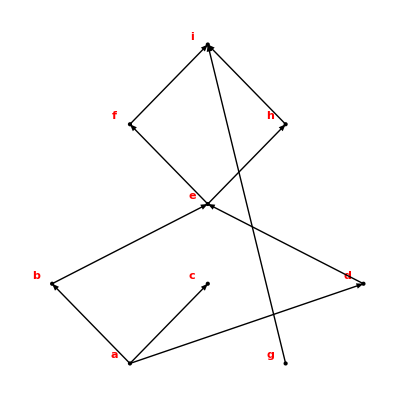

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[Do[If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```